```mathematica
trans:=(r1 - a1  Exp[I ϕ1])/(1-r1   a1  Exp[I ϕ1])       
ref:= (- t1 t2 √a1 Exp[I ϕ1/2])/(1-r1   a1  Exp[I ϕ1])
```

```mathematica
n:=3.45;
R1:=10 10^(-6);
R2:=10 10^(-6);
d1:= 2 Pi R1
d2:= 2 Pi R2
λ:=1550 10^(-9); (* resonant wavelrngth *)
Q1:=1×10^5;
Q2:=1×10^6;
α1:=(2 Pi n)/(λ  Q1)
α2:=(2 Pi n)/(λ  Q2)
a1:= Exp[- α1 d1]
a2:= Exp[- α2 d2]
t1:=√(1-r1^2)
t2:=√(1-r2^2)
t3:=√(1-r3^2)
r1:= 0.997
r2:= 0.999
r3:= 0.999
```

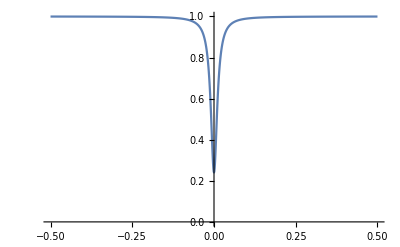

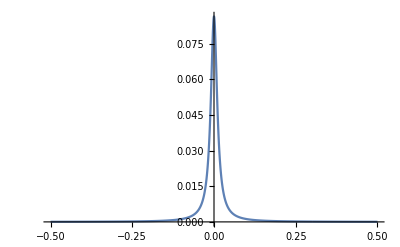

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
transdata:=Table[{ϕ1,Abs[trans]^2},{ϕ1,ϕ1min, ϕ1max, 0.001}]
refdata:=Table[{ϕ1,Abs[ref]^2},{ϕ1,ϕ1min, ϕ1max, 0.0001}]
ListLinePlot[transdata,PlotRange->{0,1}]
ListLinePlot[refdata,PlotRange->All]
```

```mathematica
FullSimplify[ComplexExpand[Im[trans]]]
FullSimplify[ComplexExpand[Re[trans]]]
```

```mathematica
trans:=(r1 - a1  (Cos[ϕ1]+ⅈ Sin[ϕ1]))/(1-r1   a1  (Cos[ϕ1]+ⅈ Sin[ϕ1]))
ref:= (-  t1 t2 √a1 Exp[I ϕ1/2])/(1-r1   a1  (Cos[ϕ1]+ⅈ Sin[ϕ1]))
retrans:=(a1 (-1+r1^2) Sin[ϕ1])/(1+a1^2 r1^2-2 a1 r1 Cos[ϕ1])
imtrans:=((1+a1^2) r1-a1 (1+r1^2) Cos[ϕ1])/(1+a1^2 r1^2-2 a1 r1 Cos[ϕ1])
reref:=-((a1^2)^(1/4) t1 t2 (Sin[ϕ1/2]+a1 r1 Sin[ϕ1/2]))/(1+a1^2 r1^2-2 a1 r1 Cos[ϕ1])
imref:= ((a1^2)^(1/4) t1 t2 (-Cos[ϕ1/2]+a1 r1 Cos[ϕ1/2]))/(1+a1^2 r1^2-2 a1 r1 Cos[ϕ1])
```

```mathematica
Print["r1=",r1,", r1d=",r1d," , r2=",r2,", r2d=",r2d""]
Print["Q1=",ScientificForm[Q1],", Q2=",ScientificForm[Q2],""]
```

```mathematica
Export["fig1.dat",transdata]
```

fig1.dat

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["fig1.dat"]]]
```